# Second Quantization Functions

This tech note introduces the QuantumFramework implementation of bosonic second quantization on a truncated Fock space. The truncation provides a finite-dimensional representation that is convenient for computation while retaining the structure of common states and operators. The examples below focus on practical workflows for building states, applying operators, and visualizing results in quantum mechanics and quantum optics.

Install and load the QuantumFramework paclet and the second-quantization subpackage (skip the install step if it is already available):

```mathematica
(*PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]*)
PacletDirectoryLoad["/Users/mohammadb/Documents/GitHub/QuantumFramework/QuantumFramework/QuantumFramework/"]
<<Wolfram`QuantumFramework`
<<Wolfram`QuantumFramework`SecondQuantization`
```

{/Users/mohammadb/Documents/GitHub/QuantumFramework/QuantumFramework/QuantumFramework/}

## Bosonic states and operators

### Fock space size and utilities

SetFockSpaceSize[size] | Sets size as the default truncation dimension ,  all the other definitions can use this default size
OperatorVariance[ψ,op] | Variance of the operator op for a state ψ

### States

FockState[n,size] | n-th Fock state in a basis of dimension size
FockState[{n_1,n_2,..},size] | Multimode Fock state with occupation numbers n_i , with each mode in a basis of dimension size 
CoherentState[size]
CoherentState[size][α] | Parametric state representing a non-normalized coherent state in a  basis of dimension size , the complex amplitude is a parameter
ThermalState[nbar,size] | Thermal mixed state with the average number of photons nbar in a  basis of dimension size
CatState[size]
CatState[size][α,ϕ] | Parametric general cat state representing a superposition of coherent states in a basis of dimension size, the complex amplitude and the phase are parameters

### Operators

AnnihilationOperator2[size, order] | Bosonic annihilation operator in a truncated Fock space
with basis dimension size and qudit order order
DisplacementOperator2[α,size, order] | Phase space displacement operator of a single mode with complex amplitude alpha , basis dimension size and qudit order order
SqueezeOperator2[ξ,size,order] | Squeeze operator of a single mode with complex parameter xi , basis dimension size  and qudit order order
QuadratureOperators2[size,order] |  X_1 and X_2 position and momentum quadrature operators with basis dimension size  and qudit order order
PhaseShiftOperator2[θ,size,order] | Phase space rotation operator with rotation angle θ, basis dimension size and qudit order order
BeamSplitterOperator2[{θ,ϕ},size,order] | Two mode beam-splitter operator, θ indicates the reflectivity, ϕ the relative phase in a basis of dimension size and qudit order order

In the sections below, we demonstrate how to use these functions in the QuantumFramework.

## Details and options

### Operators Mathematical Definitions

DisplacementOperator | Exp[α a^† -α^*a]
SqueezeOperator | Exp[1/2(ξ* a^2 - ξ  a^(†2))]
PhaseShiftOperator | Exp[ⅈ θ a^†a]
BeamSplitterOperator | Exp[θ(ⅇ^(ⅈ ϕ)a_1 a_2^†-ⅇ^(-ⅈ ϕ)a_1^†a_2)]
QuadratureOperators | X_1:1/2(a+a^†)
X_2:1/(2 ⅈ)(a-a^†)

#### Displacement operator ordering

By default, when "Ordering" is not specified, normal ordering is used. The formulas for the three orderings are shown below:

DisplacementOperator[..,"Ordering"→st] | st can be "Normal", "Weak" or "Antinormal".

For "Normal", one gets:
Exp[-|α|^2/2]Exp[α .01 a^†]Exp[-α* a]

For "Weak", one gets:
Exp[α a^†-α*a]

For "Antinormal", one gets:
Exp[|α|^2/2]Exp[-α*a]Exp[α a^†]

#### Squeeze operator ordering

By default, when "Ordering" is not specified, normal ordering is used. The formulas for the three orderings are shown below:

SqueezeOperator[…,"Ordering"→st] | st can be "Normal", "Antinormal" or "Weak". Given  ξ=rⅇ^(ⅈ θ)
for "Normal", one gets:
Exp[-1/2 ⅇ^(ⅈ θ) Tanh[r]a^(†2)]Exp[-Log[Cosh[r]](a^†a + 1/2)] Exp[1/2 ⅇ^(-ⅈ θ)Tanh[r]a^2]

For "Weak", one gets:
Exp[1/2(ξ* a^2 - ξ  a^(†2))]

For "Antinormal", one gets:
Exp[1/2 ⅇ^-ⅈθ Tanh[r]a^2]Exp[Log[Cosh[r]](a^†a + 1/2)] Exp[-1/2 ⅇ^(ⅈ θ)Tanh[r]a^(†2)]

#### Second-order coherence

G2Coherence[ψ,a] | Second-order coherence g^(2)(0) for state ψ with annihilation operator a

## Basic usage

### Setting the space size

The global variable $FockSize stores the default truncation size (dimension) of the Fock space. It is used by all second-quantization functions when the size parameter is not explicitly specified.
• Default value: 16
• Use SetFockSpaceSize[n] to change the default.
• Use SetFockSpaceSize[] to reset to 16.

Note: Larger truncation sizes improve accuracy for high photon-number states, but increase computational cost.

Show the default truncation size:

```mathematica
$FockSize
```

16

Set the truncation size to 20:

```mathematica
SetFockSpaceSize[20];
```

Show new truncation size:

```mathematica
$FockSize
```

20

Set the default size again:

```mathematica
SetFockSpaceSize[];
```

Show the current truncation size:

```mathematica
$FockSize
```

16

### Fock States

Create a single-mode Fock state with occupation number 5 using the default truncation size:

```mathematica
FockState[5]
```

QuantumState[…]

Create a single-mode Fock state with occupation number 5 using truncation size 10:

```mathematica
FockState[5,10]
```

QuantumState[…]

Create a two-mode Fock state with occupation numbers 2 and 12:

```mathematica
FockState[{2,12}]
```

QuantumState[…]

Verify the shorthand string representation matches the two-mode state:

```mathematica
FockState[{6,6}]== QuantumState["66",$FockSize]
```

True

This shorthand does not work for numbers ≥ 10 because the digits are interpreted as separate qudits:

```mathematica
FockState[{10,10}]//TraditionalForm
QuantumState["1010",$FockSize]//TraditionalForm
```

False

### Annihilation and creation operators

Create a single-mode annihilation operator with the default truncation size:

```mathematica
AnnihilationOperator[]
```

QuantumOperator[…]

Create an annihilation operator with truncation size 8 (an 8×8 matrix) using the default mode order {1}:

```mathematica
AnnihilationOperator[8]
```

QuantumOperator[…]

Create an annihilation operator acting on mode 2 using the default truncation size:

```mathematica
AnnihilationOperator[{2}]
```

QuantumOperator[…]

Create an annihilation operator with size 5 acting on mode 3:

```mathematica
AnnihilationOperator[5,{3}]
```

QuantumOperator[…]

Apply the annihilation operator to a Fock state:

```mathematica
AnnihilationOperator[][FockState[2]]//TraditionalForm
```

√2 1

Define the creation operator by taking the adjoint (SuperDagger) of the annihilation operator, then apply it to a Fock state:

```mathematica
SuperDagger[AnnihilationOperator[]]@ FockState[1] //TraditionalForm
```

√2 2

Or use the "Dagger" property directly:

```mathematica
AnnihilationOperator[]["Dagger"]@FockState[1]//TraditionalForm
```

√2 2

### Coherent state

Create a symbolic coherent state with the default truncation size:

```mathematica
CoherentState[][β]
```

QuantumState[…]

Create a symbolic coherent state with truncation size 20:

```mathematica
CoherentState[20][β]
```

QuantumState[…]

Photon-number distribution for a coherent state with α = 1.3+2ⅈ using truncation size 25:

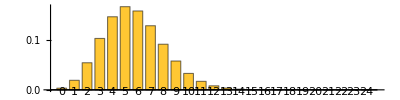

```mathematica
CoherentState[25][1.3+2ⅈ]["ProbabilityPlot",LabelStyle-> 8,AspectRatio->1/4]
```

### Cat State

Create a cat state 𝒩_α(α+ⅇ^ⅈϕ-α) with amplitude α=2+ⅈ and phase ϕ=3π/4:

```mathematica
CatState[25][2+ⅈ,3π/4]
```

QuantumState[…]

Photon distribution of the same state:

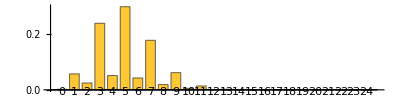

```mathematica
CatState[25][2+ⅈ,3π/4]["ProbabilityPlot",LabelStyle-> 6,AspectRatio->1/4]
```

### Thermal state

Create a thermal state with mean photon number n^—=2 using truncation size 40:

```mathematica
ThermalState[2.,40]
```

QuantumState[…]

Plot the photon-number distribution (diagonal of the density matrix):

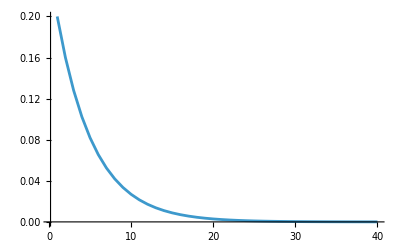

```mathematica
ListLinePlot[Diagonal[ThermalState[4,40]["DensityMatrix"]],PlotRange->All]
```

Define a parametric thermal state in terms of the mean photon number:

```mathematica
state = QuantumState[ThermalState[x,40],"Parameters"->x]
```

QuantumState[…]

Plot the entropy as a function of the mean photon number:

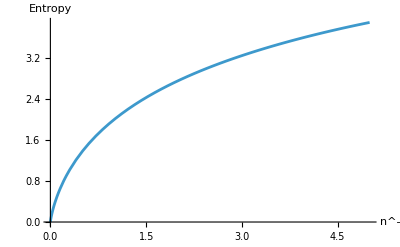

```mathematica
Plot[state[x]["Entropy"],{x,0,5},AxesLabel->{"n^—","Entropy"}]
```

### Displacement operator

Create a displacement operator with truncation size 40 and amplitude 3+ⅈ:

```mathematica
DisplacementOperator[3+ⅈ,40]
```

QuantumOperator[QuantumState[SparseArray[<1600>, {1600}], QuantumBasis[<|Input -> QuditBasis[<|{QuditName[0, Dual -> True], 1} -> SparseArray[<1>, {40}], {QuditName[1, Dual -> True], 1} -> SparseArray[<1>, {40}], {QuditName[2, Dual -> True], 1} -> SparseArray[<1>, {40}], «35», {«2»} -> <<10>>y[«2»], {QuditName[39, Dual -> True], 1} -> SparseArray[<1>, {40}]|>], «4»|>]], {«2»}]

Verify that displacing the vacuum produces a coherent state:

```mathematica
DisplacementOperator[α,40][]==CoherentState[40][α]
```

True

Specify the mode (order) of the operator with the default size, mode 2 in this case:

```mathematica
DisplacementOperator[0.5,{2}]
```

QuantumOperator[…]

### Phase shift operator

Matrix form of the phase-shift operator for truncation size 10:

```mathematica
PhaseShiftOperator[θ,10]["Matrix"]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅇ^(ⅈ θ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅇ^(2 ⅈ θ) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(3 ⅈ θ) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^(4 ⅈ θ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(5 ⅈ θ) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(6 ⅈ θ) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(7 ⅈ θ) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(8 ⅈ θ) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(9 ⅈ θ))

Effect of phase shift on a single-mode symbolic state:

```mathematica
PhaseShiftOperator[θ][QuantumState[Array[Subscript[c, #]&,$FockSize-1,0],$FockSize]]//TraditionalForm
```

c_0 0+c_1 ⅇ^(ⅈ θ)1+c_2 ⅇ^(2 ⅈ θ)2+c_3 ⅇ^(3 ⅈ θ)3+c_4 ⅇ^(4 ⅈ θ)4+c_5 ⅇ^(5 ⅈ θ)5+c_6 ⅇ^(6 ⅈ θ)6+c_7 ⅇ^(7 ⅈ θ)7+c_8 ⅇ^(8 ⅈ θ)8+c_9 ⅇ^(9 ⅈ θ)9+c_10 ⅇ^(10 ⅈ θ)10+c_11 ⅇ^(11 ⅈ θ)11+c_12 ⅇ^(12 ⅈ θ)12+c_13 ⅇ^(13 ⅈ θ)13+c_14 ⅇ^(14 ⅈ θ)14

Effect of phase shift on a two-mode superposition state:

```mathematica
PhaseShiftOperator[θ,{2}][FockState[{5,3}]+FockState[{5,6}]]//TraditionalForm
```

ⅇ^(3 ⅈ θ)53+ⅇ^(6 ⅈ θ)56

Phase shift operator coincides with the "Z" gate for qudits when the angle is 2π/n (up to conjugation):

```mathematica
With[{n=RandomInteger[{1,$FockSize-1}]},PhaseShiftOperator[2π/n,n]==QuantumOperator["Z"[n]]["Conjugate"]]
```

True

### Squeeze operator

Create a squeeze operator with complex parameter 1+ⅈ using the default size:

```mathematica
SqueezeOperator[1.+ⅈ]
```

QuantumOperator[…]

Create a two-mode state with mode 2 in a squeezed vacuum (ξ = 0.9) using truncation size 15:

```mathematica
state =SqueezeOperator[0.9,15,{2}]@FockState[{0,0},15]
```

QuantumState[…]

Plot the non-zero amplitudes of the state:

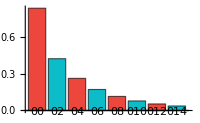

```mathematica
state["AmplitudePlot",ChartLegends->Automatic,ImageSize->200]
```

### Beam-Splitter Operator

Set a symmetric beam splitter with θ = π/4 and ϕ = π/2:

```mathematica
symmetricBS =BeamSplitterOperator[{π/4.,π/2.}]
```

QuantumOperator[…]

Transform the state |1,1⟩ with the symmetric beam splitter:

```mathematica
symmetricBS[FockState[{1,1}]]//Chop//TraditionalForm
```

(0.+0.707107 ⅈ)02+(0.+0.707107 ⅈ)20

Specify the mode order (where the operator acts) and the truncation size:

```mathematica
BeamSplitterOperator[{0.2,0.9},6,{1,3}]
```

QuantumOperator[…]

#### BeamSplitter operator: Method option

BeamSplitterOperator supports two computation methods via the Method option. The default is MatrixExp which uses direct matrix exponentiation; Recurrence uses an efficient recurrence relation for the beam splitter matrix elements. Performance can vary depending on whether the angle arguments are numeric or exact/symbolic.

Use the "Recurrence" method with exact angles:

```mathematica
BeamSplitterOperator[{π/4,π/2},Method->"Recurrence"][FockState[{1,1}]]//TraditionalForm
```

ⅈ/(√2)02+ⅈ/(√2)20

### OperatorVariance

Calculate the variance of the quadrature operators for the ground state:

```mathematica
OperatorVariance[FockState[0],#]& /@ QuadratureOperators[]
```

{1/4,1/4}

A Fock state has a definite number of photons, so the variance of the number operator is zero:

```mathematica
SetFockSpaceSize[];
With[{a=AnnihilationOperator[]},OperatorVariance[FockState[2],SuperDagger[a]@a]]
```

0

### G2Coherence (Second-Order Coherence)

The function G2Coherence computes the equal-time second-order coherence g\[Superscript](2)(0), which characterizes the photon statistics of a quantum state. It is defined as:

g^(2)(0)=⟨a^†a^†a a⟩/(⟨a^†a⟩^2)
Physical interpretation:
• g^(2)=1: Poissonian statistics (coherent light)
• g^(2)<1: Sub-Poissonian (antibunching, nonclassical light)
• g^(2)>1: Super-Poissonian (bunching, thermal light)
• g^(2)=0: Single-photon state

For a coherent state, g^(2)=1:

```mathematica
G2Coherence[CoherentState[][2.],AnnihilationOperator[]]
```

0.999959

For a Fock state |n⟩ with n > 0, g^(2)=1-1/n:

```mathematica
G2Coherence[FockState[3],AnnihilationOperator[]]
```

2/3

For a thermal state with mean photon number n̄, g^(2)=2:

```mathematica
G2Coherence[ThermalState[2.],AnnihilationOperator[]]
```

1.93094

It is not exactly 2 because of truncation: the thermal distribution has significant weight at photon numbers beyond the cutoff.

The single photon state |1⟩ has g^(2)=0 (perfect antibunching):

```mathematica
G2Coherence[FockState[1],AnnihilationOperator[]]
```

0

### Quadrature Operators

Compute the commutator of the quadrature operators. It should be ⅈ/2 1; any small deviation in the last term is expected due to truncation:

```mathematica
(Commutator@@ QuadratureOperators[])//TraditionalForm
```

ⅈ/2 00+ⅈ/2 11+ⅈ/2 22+ⅈ/2 33+ⅈ/2 44+ⅈ/2 55+ⅈ/2 66+ⅈ/2 77+ⅈ/2 88+ⅈ/2 99+ⅈ/2 1010+ⅈ/2 1111+ⅈ/2 1212+ⅈ/2 1313+ⅈ/2 1414-(15 ⅈ)/21515

Expectation value of  ⟨X_1^2⟩ for Fock state 3:

```mathematica
FockState[3]["Dagger"][(QuadratureOperators[][[1]]^2)[FockState[3]]]["Scalar"]
```

7/4

### Mode Ordering (Multimode Systems)

Displacement and squeeze operators can be defined with different orderings. Use the "Ordering" option to choose "Weak", "Normal", or "Antinormal". In the infinite-dimensional limit these are equivalent, but in a truncated space the numerical error depends on the ordering, so one choice may be more accurate for a given calculation.

Many operators accept an optional order parameter that specifies which mode(s) the operator acts on in a multimode system. The order is a list of positive integers.
• Default: {1} (single mode, acts on mode 1)
• Two modes: {1,2} or {2,3} etc.
The order parameter is essential for:
• Creating operators that act on specific modes in a tensor-product space.
• Building multimode quantum circuits (e.g., beam splitters coupling modes 1 and 2).

Single-mode operator with explicit order:

```mathematica
AnnihilationOperator[{2}]
```

QuantumOperator[…]

n_1,n_2 a_2 n_1,n_2=√n_2 n_1,n_2-1

Verify the action numerically:

```mathematica
AnnihilationOperator[{2}][FockState[{3,5}]]==√5 FockState[{3,5-1}]
```

True

Two-mode beam splitter acting on modes 1 and 3:

```mathematica
BeamSplitterOperator[{π/4,π/2},{1,3},Method->"Recurrence"][FockState[{1,3,1}]]//TraditionalForm
```

ⅈ/(√2)032+ⅈ/(√2)230

Displacement operator on mode 3:

```mathematica
DisplacementOperator[1.5,8,{3}]
```

QuantumOperator[…]

Note: When using mode ordering, all operators in a calculation should use consistent mode assignments. The order parameter does NOT change the Fock space dimension—it only labels which mode the operator acts on.

### Error Messages

The following error messages may be generated by second-quantization functions:

FockState::clip | Issued when the Fock state index is outside the valid range [0, size-1]. The index is clipped to the nearest valid value.
FockVals::len | Issued when multimode Fock state values contain invalid (negative or too large) integers.
DisplacementOperator::invalidorder | Issued when the "Ordering" option is not "Normal", "Weak", or "Antinormal".
SqueezeOperator::invalidorder | Issued when the "Ordering" option is not "Normal", "Weak", or "Antinormal".
BeamSplitterOperator::badmethod | Issued when the Method option is not "MatrixExp" or "Recurrence".

Example: FockState index clipping

```mathematica
FockState[100,16]
```

FockState::clip: Index 100 was outside the valid range {0, 15} and has been clipped.

QuantumState[…]

### Ordering option

Check unitarity of the displacement operator using "UnitaryQ" for α = 0.5+ⅈ. In this truncation, weak ordering gives a more accurate check:

```mathematica
DisplacementOperator[0.5+ⅈ]["UnitaryQ"]
```

False

Repeat the check using weak ordering:

```mathematica
DisplacementOperator[0.5+ⅈ,"Ordering"->"Weak"]["UnitaryQ"]
```

True

For a squeezed vacuum state with ξ = 1.5 +0.5 ⅈ and size = 20 compare the numerical error of "Weak" and "Normal" orderings against the analytic expression. For this value of ξ, the truncation size is not sufficient for the weak-ordered operator, and the normal-ordered one is more accurate.

Amplitudes obtained from a known analytic formula:

```mathematica
analytic = 1/√Cosh[Abs[ξ]]Table[√((2m)!)/(2^m m!)(-1)^m ⅇ^(ⅈ m Arg[ξ])Tanh[Abs[ξ]]^m,{m,0,9}]/.ξ->(1.5+0.5ⅈ);
```

Compute absolute errors:

```mathematica
absoluteErrors= (SqueezeOperator[1.5+0.5ⅈ,20,"Ordering"->#][]["AmplitudeList"]-analytic)& /@{"Normal","Weak"};
```

Show the results:

```mathematica
TableForm[absoluteErrors//Transpose,TableHeadings->{Table[StringForm["|``⟩",i],{i,0,20,2}], {"Normal","Weak"}}]
```

| Normal | Weak
|0⟩ | 1.44329×10^-15 | -0.000275202
|2⟩ | -9.99201×10^-16-3.05311×10^-16 ⅈ | -0.00321923-0.00107308 ⅈ
|4⟩ | 6.10623×10^-16+3.88578×10^-16 ⅈ | -0.0120623-0.00904674 ⅈ
|6⟩ | -3.88578×10^-16-4.44089×10^-16 ⅈ | -0.0214194-0.0309391 ⅈ
|8⟩ | 1.38778×10^-16+3.88578×10^-16 ⅈ | -0.0176372-0.0604703 ⅈ
|10⟩ | 3.98986×10^-17-3.33067×10^-16 ⅈ | 0.00310254-0.0817001 ⅈ
|12⟩ | -1.38778×10^-16+3.33067×10^-16 ⅈ | 0.0330558-0.0878983 ⅈ
|14⟩ | 2.22045×10^-16-2.498×10^-16 ⅈ | 0.0645373-0.0795701 ⅈ
|16⟩ | -1.94289×10^-16+1.11022×10^-16 ⅈ | 0.0909739-0.0580024 ⅈ
|18⟩ | 1.94289×10^-16-4.85723×10^-17 ⅈ | 0.10781-0.027051 ⅈ

### Applications: States and operators

### Mean number of photons

Define the annihilation operator and create a random pure state:

```mathematica
a:=AnnihilationOperator[]
ψ = QuantumState["RandomPure",$FockSize];
```

Compute the mean number of photons using QuantumMeasurementOperator:

```mathematica
(QuantumMeasurementOperator[SuperDagger[a]@a][ψ])["Mean"]
```

7.2643

Equivalent bracket notation ⟨ ψ |a^†a|ψ⟩ :

```mathematica
Chop[( SuperDagger[ψ]@(SuperDagger[a]@a)@ψ )["Scalar"]]
a[ψ]["Norm"]^2
```

7.2643

7.2643

Using the probabilities in the diagonal of the density matrix:

```mathematica
Chop@Dot[Range[0,$FockSize-1],Diagonal@ψ["DensityMatrix"]]
```

7.2643

### Heisenberg evolution of annihilation operator

In the Heisenberg picture, the annihilation operator evolves as â(t)=â ⅇ^(-ⅈ ω t). We can reproduce this using super-operators in the framework.

Define the Hamiltonian:

```mathematica
H = ℏ ω (SuperDagger[a]@a+1/2);
```

Construct the evolution super-operator:

```mathematica
expℋ =MatrixExp[-ⅈ QuantumOperator["Hamiltonian"[H/ℏ]]t];
```

Evolve the operator:

```mathematica
heisenbergAnnihilation =Simplify[expℋ["Dagger"][a["MatrixQuantumState"]]["Operator"],{t,ω}∈ Reals];
```

Compare the result to the known result of quantum mechanics:

```mathematica
a ⅇ^(-ⅈ ω t)==heisenbergAnnihilation
```

True

## Quasi-probability Representations

Two phase-space quasi-probability representations are included: Wigner and HusimiQ. They are used extensively in quantum mechanics and quantum optics. Each is computed numerically on a grid of phase-space points and returns an interpolating function. Glauber representation is not included because, for a general state, a stable numerical algorithm is not feasible due to its singularities.

WignerRepresentation[ψ,{xmin,xmax},{pmin,pmax},opts] | Computes the Wigner quasi-probabilty representation of a quantum state ψ , in a phase space rectangular region defined by the given limits of  x and p
HusimiQRepresentation[ψ,{xmin,xmax},{pmin,pmax},opts] | Computes the Husimi Q function representation of a quantum state ψ  , in a phase space rectangular region defined by the given limits of x and p

In the sections below, we demonstrate how to use these functions in the QuantumFramework.

### Examples

#### Ground state Wigner Representation:

Compute the Wigner representation on the square region [-4, 4] × [-4, 4]:

```mathematica
wig = WignerRepresentation[FockState[0],{-4,4},{-4,4}];
```

Visualize the function in 3D:

```mathematica
Plot3D[
wig[x,p],{x,-4,4},{p,-4,4},
ColorFunction->"Rainbow",
PlotRange->All,
PlotLegends->Automatic,
PlotPoints->80
]
```

-Graphics3D-

#### HusimiQ Representation of a Fock state

Compute the HusimiQ representation for a Fock state with n = 4:

```mathematica
husi = HusimiQRepresentation[FockState[4],{-4,4},{-4,4}];
```

Visualize the density plot of the representation:

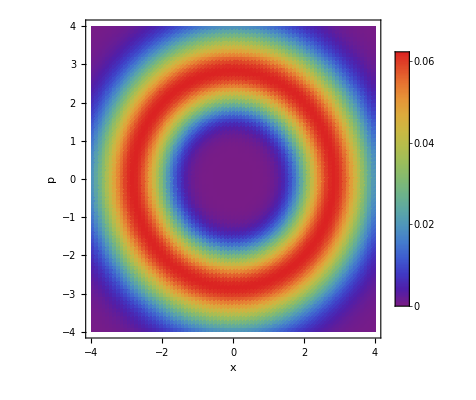

```mathematica
DensityPlot[
husi[x,p],{x,-4,4},{p,-4,4},
ColorFunction->"Rainbow",
PlotRange->All,
PlotLegends->Automatic,
PlotPoints->80,
FrameLabel->{"x","p"}
]
```

## Quasi-probability representations: Applications and options

### Applications

### Expectation values

Compute the Wigner function for the Fock state |2⟩:

```mathematica
wig = WignerRepresentation[FockState[2],{-5,5},{-5,5}];
```

Phase space integral:

```mathematica
NIntegrate[wig[x,p],{x,-4,4},{p,-4,4},AccuracyGoal->4]
```

0.999984

Compute the expectation value ⟨x^4⟩:

```mathematica
NIntegrate[x^4 wig[x,p],{x,-4,4},{p,-4,4},AccuracyGoal->4]
```

9.74749

#### Marginal distributions

Compute the Wigner function for a coherent state with α=1:

```mathematica
wig = WignerRepresentation[CoherentState[][1.]["Normalize"],{-4,4},{-4,4}]
```

InterpolatingFunction[…]

Visualize momentum distribution:

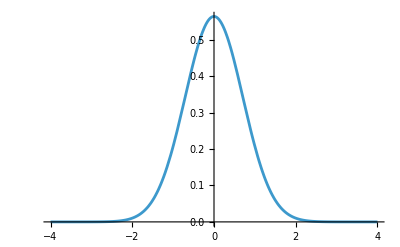

```mathematica
Plot[Evaluate[Integrate[wig[x,p],{x,-4,4}]],{p,-4,4}]
```

Visualize position distribution:

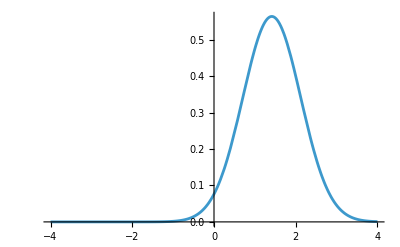

```mathematica
Plot[Evaluate[Integrate[wig[x,p],{p,-4,4}]],{x,-4,4}]
```

### Squeezed vacuum Wigner Representation

Wigner representation of a squeezed vacuum state with parameter ξ = 0.5:

```mathematica
squeezedVacuumFunc = WignerRepresentation[SqueezeOperator[0.5][],{-4,4},{-4,4}];
```

Plot the function; the nonclassical quadrature behavior of squeezed states is visible:

```mathematica
Plot3D[
squeezedVacuumFunc[x,p],{x,-4,4},{p,-4,4},
ColorFunction->"SunsetColors",
PlotRange->All,
PlotLegends->Automatic,
PlotPoints->80
]
```

-Graphics3D-

### Options

"GaussianScaling" | √2 | Scaling factor of the representation
"GridSize" | 100 | Granularity of the sampling

#### Scaling of the representation for ground state

Set the Gaussian scaling parameter to 0.5:

```mathematica
wig = WignerRepresentation[FockState[0],{-4,4},{-4,4},"GaussianScaling"-> 0.5];
```

Visualize the result:

```mathematica
Plot3D[wig[x,p],{x,-4,4},{p,-4,4},
ColorFunction->"Rainbow",
PlotRange->All,
PlotPoints->80,
PlotLegends->Automatic,
ImageSize->200]
```

-Graphics3D-

#### Using GridSize

Compute the Wigner function value at the origin for the Fock state |2⟩ using a grid size of 140:

```mathematica
wig = WignerRepresentation[FockState[2],{-6,6},{-6,6},"GridSize"->140];
wig[0,0]
```

0.318182

A grid size of 20 is insufficient for this region and yields noticeable numerical error:

```mathematica
wig2 = WignerRepresentation[FockState[2],{-6,6},{-6,6},"GridSize"->20];
wig2[0,0]
```

0.126233

The exact value from the analytic expression is:

```mathematica
exact =1/π ⅇ^(-(x^2+p^2))LaguerreL[2,2(x^2+p^2)]/.{x->0.08,p->0};
```

Compare absolute errors:

```mathematica
{exact-wig[0,0],exact-wig2[0,0]}
```

{0.000127758,0.192076}

## Advanced examples

### Decay of a coherent state

Consider ℋ= ω (â)^†â  with Lindblad jump operator L_1 = √γ â (single-photon loss channel), and set ω = 1

Define the annihilation operator and use a coherent state with |α| = 2 as the initial state:

```mathematica
a:=AnnihilationOperator[];
SetFockSpaceSize[15];
α = 2 Exp[I RandomReal[{0,2Pi}]];
coherent := CoherentState[]["Normalize"];
ρ0 = coherent[α];
```

Set the decay rate γ:

```mathematica
γ = RandomReal[{1,2}];
```

Define the Hamiltonian including photon loss:

```mathematica
ℋ = QuantumOperator["Hamiltonian"[SuperDagger[a]@a,{a},{γ}]];
```

State evolution:

```mathematica
ρt =QuantumEvolve[ℋ,ρ0,t];
```

Plot the mean photon number as a function of time:

```mathematica
meanPhotonPlot =Plot[Chop[Range[0,$FockSize-1].Diagonal[ρt[t]["DensityMatrix"]]],{t,0,1},];
```

Plot the fidelity with respect to the analytic expression:

```mathematica
fidelityPlot =Plot[QuantumSimilarity[coherent[α ⅇ^(-ⅈ t) ⅇ^(-1/2 t γ)],ρt[t]],{t,0,1},];
```

Show the results:

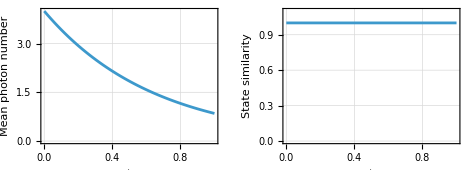

```mathematica
Labeled[GraphicsRow[{meanPhotonPlot,fidelityPlot}],]
```

### Optical balance

Consider the following master equation, which balances a driving field Hamiltonian and single-photon loss:

(ⅆ ρ)/ⅆt= -ⅈg[â+(â)^†,ρ̂]+γ/2(2 â ρ̂(â)^†-(â)^†â ρ̂-ρ̂(â)^†â)

Set the drive strength g:

```mathematica
g = RandomReal[{1, 2}];
```

Random initial state:

```mathematica
ρ0 = QuantumState["RandomPure",$FockSize];
```

Set up the master equation:

```mathematica
ℋ= QuantumOperator["Hamiltonian"[g(a+a["Dagger"]),{a},{γ}]];
```

Numerical evolution from t_i=0  to t_f=3  :

```mathematica
ρt=QuantumEvolve[ ℋ,ρ0,{t,0,3}];
```

Steady state solution is a coherent state with amplitude α = -2ⅈ g/γ via phase-space integration:

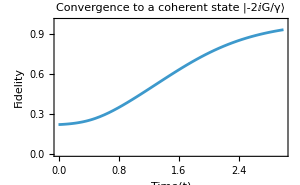

```mathematica
Plot[QuantumSimilarity[ρt[t],coherent[-I 2g/γ]],{t,0,3},]
```

For the initial state ρ̂(0) = |0⟩ ⟨0|, the system evolves to the coherent state | -ⅈ g t ⟩⟨- ⅈ g t | for short times; the complex amplitude is independent of γ.

Initial state:

```mathematica
ρ0 = QuantumState["0",$FockSize];
```

Evolved state:

```mathematica
ρt =QuantumEvolve[ℋ,ρ0,{t,0,1}];
```

Photon number expectations and fidelity:

```mathematica
time = Range[0,0.8,0.02];
qs = QuantumSimilarity[coherent[-I g #],ρt[#]]& /@ time;
meanN = Chop[Range[0,$FockSize-1].Diagonal[ρt[#]["DensityMatrix"]]]& /@ time ;
```

Plot both quantities versus time:

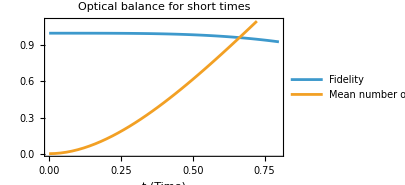

```mathematica
ListLinePlot[{Thread[{time,qs}],Thread[{time,meanN}]},]
```

### Jaynes-Cummings Model: Calculating the unitary

Define the basis and the relevant operators:

```mathematica
SetFockSpaceSize[32];
atomBasis = QuantumBasis[{"e","g"}];
σplus =  QuantumOperator["+",atomBasis];
σminus = QuantumOperator["-",atomBasis];
a := AnnihilationOperator[{2}];
```

Free Hamiltonian  ℋ_0= ℏν(â)^†â+1/2 ℏωσ_z:

```mathematica
H0 = QuantumOperator[h ν SuperDagger[a]@a+1/2 h ω QuantumOperator["Z",atomBasis],"Parameters"->{ν,ω}];
```

Atom-field interaction term ℋ_I= ℏg(σ_+â+σ_-(â)^†):

```mathematica
H1=h g(σplus@a+σminus@SuperDagger[a]);
```

Going to the interaction picture at resonance, we get a time-independent Hamiltonian:

```mathematica
HInteract=MatrixExp[I H0/h t]@H1@MatrixExp[-I H0/h t];
U=MatrixExp[-I HInteract[ν,ν]/h t];
```

### Jaynes-Cummings Model: Evolving states

#### Fock State

Rabi oscillations when the field is initially in a Fock state

```mathematica
ψ0 =QuantumState["1", atomBasis]// FockState[1];
ψt = U @ ψ0
```

QuantumState[…]

Find the probability of the atom being in the excited state:

```mathematica
proj =QuantumOperator[{{1,0},{0,0}},atomBasis];
probE =(QuantumMeasurementOperator[proj]@ ψt)["Mean"];
```

Plot the result:

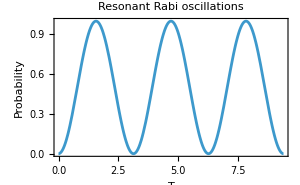

```mathematica
Plot[probE /. g->1 ,{t,0,3π},]
```

#### Coherent state: Collapse and revivals

Define the initial state |ψ_0⟩ = |g⟩|α⟩ with |α|=4 and evolve it (we use a random α):

```mathematica
α = 4 Exp[I RandomReal[{0, 2 π}]];
ψ0=QuantumState["1",atomBasis]//CoherentState[][α]["Normalize"];
ψt = QuantumState[U @ ψ0,"Parameters"->{g,t}];
```

Extracting the coefficients  c_e and c_g for all n as a function of time:

```mathematica
{cet[t_], cgt[t_]} = Values[(#["Dagger"]@ψt[1, t])["Amplitudes"]] & /@ atomBasis["BasisStates"];
```

Plotting the population inversion  W(t)=∑_n |c_(e,n)(t)|^2-|c_(g,n)(t)|^2

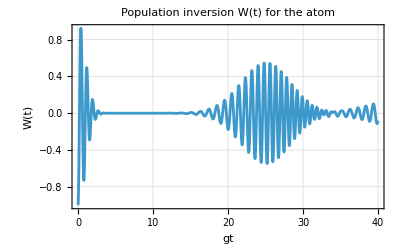

```mathematica
Plot[Total @(Abs[cet[t]]^2-Abs[cgt[t]]^2),{t,0,40},]
```

#### Atom "thermalization" (atom interacting with a thermal state field)

Atom initially in 1/(√2)(|g⟩+|e⟩) and field in a thermal state with n̄=5:

```mathematica
ρ0 = QuantumState["+",atomBasis]//ThermalState[5.];
```

Evolve the density matrix ρ(t) =Û(t) ρ(0) (Û)^†(t) . We use shortcut notation applied to matrix states:

```mathematica
ρt  = QuantumState[SuperDagger[U][ρ0],"Parameters"->{g,t}];
```

Reduced density matrix of the atom:

```mathematica
atomMatrix =Normal[QuantumPartialTrace[ρt[1,t],{2}]["DensityMatrix"]]//ComplexExpand//Simplify;
```

Plot two components of the matrix:

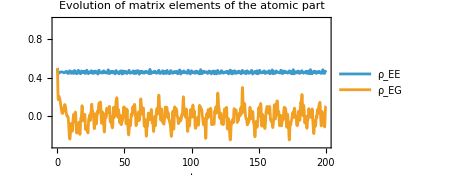

```mathematica
Plot[Evaluate[atomMatrix[[1,{1,2}]]],{t,0,200},]
```

Atom gets "thermalized"; the time-average of the coherences → 0:

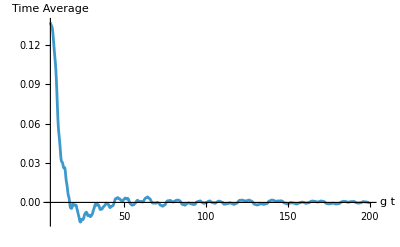

```mathematica
timeAverages = Integrate[(atomMatrix[[1,2]]),{t,0,tf}]/tf;
Plot[timeAverages,{tf,5,200},]
```

### Jaynes-Cummings with dissipation

Ĥ= ℏν(â)^†â+1/2 ℏωσ_z+ℏg(σ_+â+σ_-(â)^†)
ⅆρ/ⅆt= -ⅈ/ℏ[Ĥ, ρ]+ℒ_decay(ρ)+ℒ_loss(ρ)

where ℒ_decay,ℒ_loss are the master equation terms related to Lindblad jump operators L_1=√γ_1(σ_-⊗ ℐ) and L_2=√γ_2(ℐ ⊗ â), consider the initial state |e⟩|n⟩ with n=2.

Parameter setting:

```mathematica
SetFockSpaceSize[8];
ν = 10.;   (* field frequency *)
ω = 10.;   (* atomic frequency *)
gc = 15.; (* interaction coupling strength *)
ψ0 = QuantumState["0",atomBasis]//FockState[2];
tf=1;
```

Hamiltonian definition:

```mathematica
H =  ν SuperDagger[a]@a+ 1/2 ω QuantumOperator["Z",atomBasis]+gc (σplus@a+σminus@SuperDagger[a]);
```

Jump operators:

```mathematica
decayAtom = σminus@QuantumOperator["I"[$FockSize],{2}];
lossField = QuantumOperator["I",atomBasis]@a;
```

Helper definition to get the probability of finding the atom in the excited state in a time window:

```mathematica
atomProb[evolved_,tf_] := Table[{t, QuantumPartialTrace[evolved[t], {2}]["DensityMatrix"][[1, 1]] // Chop}, {t, 0, tf, 0.01}]
```

Compute the evolution for different damping parameters γ=γ_1=γ_2, and record the probability of finding the atom in the excited state:

```mathematica
probsE = Table[ℋ = QuantumOperator["Hamiltonian"[H, {decayAtom, lossField}, {x, x}]];
   evolved = QuantumEvolve[ℋ, ψ0, {t, 0, 1}];
   atomProb[evolved,tf],
   {x, {0.8, 0.4, 0.2}}];
```

Damped Rabi oscillations:

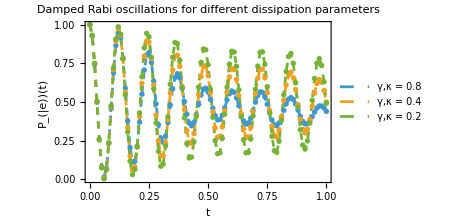

```mathematica
ListLinePlot[probsE,]
```

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

Wolfram/QuantumFramework

Wolfram`QuantumFrameworkLoader`

Wolfram/QuantumFramework/tutorial/SecondQuantization

### Keywords

Second Quantization

Fock Space

Quantum Optics